# Rate Equation

The eigen value of R, must contains 0, and 
if all eigenvalue are negative for non-explosive solution.
  thus, at time infinity, only 1 component of F is 1
  the finial poplation is the eigne vector of null space

```mathematica
Clear[R,P,F]
```

```mathematica
R={
{-20,0,0,0,10},
{1,-2,0,2,0},
{10,0,-10,0,0},
{1,0,0,-1,0},
{8,2,10,-1,-10}};
R//MatrixForm
{"Check sum",Table[Sum[R[[i,j]],{i,1,Length[R]}],{j,1,Length[R]}]}
{"Check sum",Table[Sum[R[[i,j]],{j,1,Length[R]}],{i,1,Length[R]}]}
{v,G}=Eigensystem[R]//N;
P=Transpose[G];
P.F.Inverse[P]//N//Chop//MatrixForm;
F=Table[If[i==j,Chop[v[[i]]],0],{i,1,Length[R]},{j,1,Length[R]}];
{"D",F//TableForm}
Normalize[Flatten[NullSpace[R]],Total]
{"Trace[R]",Tr[R]}
```

(-20 | 0 | 0 | 0 | 10
1 | -2 | 0 | 2 | 0
10 | 0 | -10 | 0 | 0
1 | 0 | 0 | -1 | 0
8 | 2 | 10 | -1 | -10)

{Check sum,{0,0,0,0,0}}

{Check sum,{-10,1,0,0,9}}

{D,-19.75+3.23114 ⅈ | 0 | 0 | 0 | 0
0 | -19.75-3.23114 ⅈ | 0 | 0 | 0
0 | 0 | -1.75004+0.428129 ⅈ | 0 | 0
0 | 0 | 0 | -1.75004-0.428129 ⅈ | 0
0 | 0 | 0 | 0 | 0}

{2/13,3/13,2/13,2/13,4/13}

{Trace[R],-43}

{{0.,0,0,0,0},{0,0.,0,0,0},{0,0,0.,0,0},{0,0,0,0.,0},{0,0,0,0,1}}

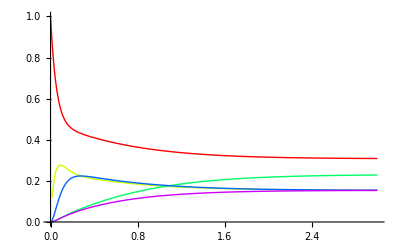

```mathematica
Limit[MatrixExp[F t],t->∞]
(*Limit[MatrixExp[R t],t-> ∞]
k=Normalize[Table[RandomInteger[{0,2}],{i,1,Length[R]}]]*)
Plot[Evaluate[MatrixExp[R t].UnitVector[Length[R],5]],{t,0,3},PlotRange->All,PlotStyle->Table[Hue[i/Length[R]],{i,1,Length[R]}]]
```

## Related to Markov Matrix

```mathematica
R={
{-2,1,0},
{1,-1,1},
{1,0,-1}};
R//MatrixForm
Det[R]
NullSpace[R]
Mr=MatrixExp[R]//N;
Mr//MatrixForm
Table[Sum[Mr[[i,j]],{i,1,Length[Mr]}],{j,1,Length[Mr]}]
Limit[MatrixPower[Mr,n],n->∞]//Chop//MatrixForm
```

(-2 | 1 | 0
1 | -1 | 1
1 | 0 | -1)

0

{{1,2,1}}

(0.283834 | 0.283834 | 0.148499
0.432332 | 0.567668 | 0.432332
0.283834 | 0.148499 | 0.419169)

{1.,1.,1.}

(0.25+1.55249×10^-10 ⅈ | 0.25-1.55249×10^-10 ⅈ | 0.25+1.55249×10^-10 ⅈ
0.5+3.10498×10^-10 ⅈ | 0.5-3.10498×10^-10 ⅈ | 0.5+3.10498×10^-10 ⅈ
0.25+1.55249×10^-10 ⅈ | 0.25-1.55249×10^-10 ⅈ | 0.25+1.55249×10^-10 ⅈ)

## Others

```mathematica
Array[H,{4,4}];
V[i_,j_,r_,s_]:=H[i,r]KroneckerDelta[s,j]-H[s,j]KroneckerDelta[r,i]
```

```mathematica
V[1,1,3,2]
V[1,1,2,3]
```

0

0

```mathematica
Table[V[i,j,i,i]==0,{i,1,4},{j,1,4}]
```

{{True,-H[1,2]==0,-H[1,3]==0,-H[1,4]==0},{-H[2,1]==0,True,-H[2,3]==0,-H[2,4]==0},{-H[3,1]==0,-H[3,2]==0,True,-H[3,4]==0},{-H[4,1]==0,-H[4,2]==0,-H[4,3]==0,True}}

```mathematica
Sz={{1,0},{0,-1}};
Sx={{0,1},{1,0}};
```

```mathematica
MatrixExp[-ⅈ Sz θ].Sx.MatrixExp[ⅈ Sz θ]
```

{{0,ⅇ^(-2 ⅈ θ)},{ⅇ^(2 ⅈ θ),0}}